## World’s fastest non-trivial FDN mixing function

The core function in this transform is a single level of recursion of the Fast Hadamard Transform, which we denote by the function hml below. This function writes

```mathematica
(* Hadamard level function *)
hml[v_]:=Join[
Drop[v,Length[v]/2]+Drop[v,-Length[v]/2],
Drop[v,Length[v]/2]-Drop[v,-Length[v]/2]
]

wfmf[v_]:=
RotateLeft[
hml[v],
1]/2

wfmf2[v_]:=
RotateLeft[
hml[
Join[
hml[Drop[v,Length[v]/2]],
hml[Drop[v,-Length[v]/2]]
]
],
1]/2
wfmf2[{1,0,0,0}]
```

{-1/2,1/2,-1/2,1/2}

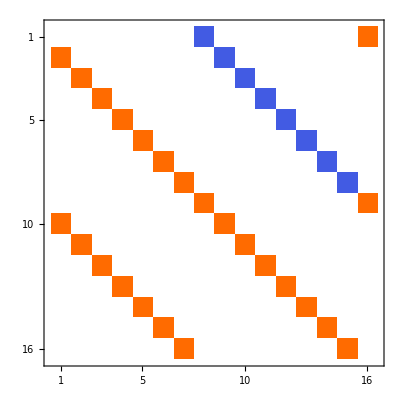

```mathematica
standardBasis[m_,N_]:=Table[If[n==m,1,0],{n,1,N}]
m = wfmf /@ IdentityMatrix[16];
m//MatrixPlot
```